# Arm state visualization

## Import

```mathematica
ClearAll["Global`*"]
Clear["Global`*"]
<<"PlotLegends`"

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_16__19_07_28"; (* range: 40 deg *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_17__09_34_18";(* range: 50 deg *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_17__13_32_26";(* range: 60 deg 2*)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_17__12_20_59";(* range: 60 deg *)

 dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_18__00_17_05";(* range: 50 deg, 2 dist *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_18__00_34_50";(* range: 50 deg, 2 dist *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_18__17_06_21";(* range: 50 deg, 1 dist again*)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_16__15_57_23";(* range: 50 deg *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_25__15_59_49"; (*  *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_25__16_00_05"; (* 0.781 *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_26__10_54_39";(* Long line: Inc. 0.82 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_26__12_51_07";(* Long line: 0.8823 *)
(*dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_26__12_51_33";(* Long line: 0.882 *)*)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_10_07__10_29_27";(* Long line: 0.748 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_10_07__15_58_20";(* Long line: 0.703 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_10_07__20_31_38";(* Long line: 0.703 *)

(* I4H6 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp4H6/13_10_09__20_48_16";(* Total KO: F0.81 !!! *)

(* I3H6 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/13_10_10__08_12_22";(* 0.8 KO: F0.82, large curvature at end *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/13_10_10__18_56_43";(* 0.8 KO, inc: F0.86, quite curved at end *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/13_10_11__08_47_14"; (* Total KO, inc: F0.877, still curved *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/13_10_14__17_48_53";(* Total KO, inc: F0.868, little curvature !*)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/ConMin/13_10_16__20_22_57";(* COnn mi.*)

(* I3H4 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H4/13_10_10__21_18_25";(* 0.8 KO: F0.76, works a little *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H4/13_10_11__00_52_23";(* 0.8 KO: F0.72, not very good *)

(* 2 positions, no ko *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/NoKo/13_10_17__13_03_34";(* *)

(* 2 positions *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_10_26__12_11_44";(* *)
(*dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_10_27__11_11_13";(* *)*)



SetDirectory[dirName];
all=Import["State.txt", "Table"];
varNames=all[[1]]
data = all[[2;;-2]];
numVars=Dimensions[varNames];
numData=Length[data]

fitXml = Import["GA_Progress.xml"];
fitness=Cases[fitXml,XMLElement["Generation",{_,"BestFitness"->fit_,_},___]->fit,Infinity];
avgfitness=Cases[fitXml,XMLElement["Generation",{_,_,"AverageFitness"->fit_},___]->fit,Infinity];
fitness=ToExpression[fitness];
avgfitness=ToExpression[avgfitness];
font="Arial";
```

{NeuralExtInput0,NeuralExtInput1,NeuralExtInput10,NeuralExtInput2,NeuralExtInput3,NeuralExtInput4,NeuralExtInput5,NeuralExtInput6,NeuralExtInput7,NeuralExtInput8,NeuralExtInput9,NeuralOutput0,NeuralOutput1,NeuralOutput10,NeuralOutput2,NeuralOutput3,NeuralOutput4,NeuralOutput5,NeuralOutput6,NeuralOutput7,NeuralOutput8,NeuralOutput9,NeuralState0,NeuralState1,NeuralState10,NeuralState2,NeuralState3,NeuralState4,NeuralState5,NeuralState6,NeuralState7,NeuralState8,NeuralState9,accelerationElbow,accelerationShoulder,angleElbow,angleShoulder,coriolisElbow,coriolisShoulder,dampingElbow,dampingShoulder,elbX,elbY,gravityElbow,gravityShoulder,inertiaElbow,inertiaShoulder,interactionElbow,interactionShoulder,lineX1,lineX2,lineY1,lineY2,torqueElbow,torqueShoulder,velocityElbow,velocityShoulder,x,y}

24000

## Fitness

{6000}

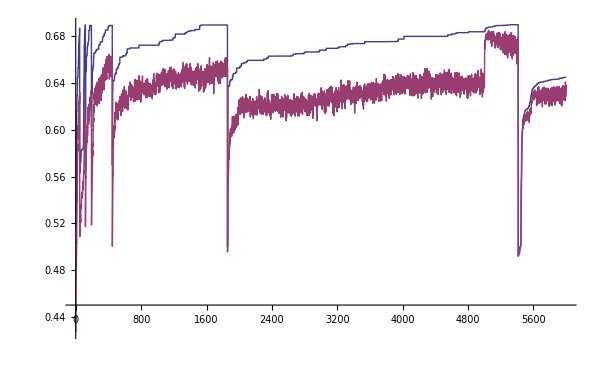

0.689934

```mathematica
Dimensions[fitness]

fit={fitness,avgfitness};
fitP =ListLinePlot[fit,PlotRange->All,ImageSize->600]
maxFit = Max[fitness]
```

## Config

```mathematica
plotOptions = {PlotRange->All};

numNeurons = 11;

dt =1/200;
T=12.0;
skip=0.0;
numTrials = Round[numData/(T/dt)]

SetTrial[trial_]:=Module[{},
t0=1+(trial*T+skip)/dt;
tn= t0+((T-skip)/dt)-1;
time=Range[tn-t0]*dt;
];

NtoI[name_]:=Position[varNames, name][[1,1]];

NtoD[name_]:=Table[data[[i,NtoI[name]]],{i,t0,tn-1}];

TimePlot[name_, options_, Scale_:1] := Module[{},
ListLinePlot[Transpose[{time,Scale*NtoD[name]}], Join[options,plotOptions]]
];

TimePlotT[name_, options_, tr_] := Module[{},SetTrial[tr];TimePlot[name,options,1]];

(*Inflate[x_,f_]:=If[x<0,(1+f)*)

XYPlot[tr_,name1_,name2_, options_] :=Module[{},
SetTrial[tr];
ListPlot[Transpose[{NtoD[name1],NtoD[name2]}], Join[options,plotOptions]]
];

XYPlotTime[tr_,name1_,name2_, options_]:=Module[{},
xy=XYPlot[tr,name1,name2,Join[options,{Joined->False}]]/.Point[args___]:>Point[args,VertexColors->Map[GrayLevel,0.9*Range[0,1,1/Length[time]]]];
line = XYPlot[tr,name1,name2,Join[options,{Joined->True,PlotStyle->Red}]];
Show[line,xy]
];

MinExpand[x_,f_]:=If[x>=0,(1-f)*x,(1+f)*x];
MaxExpand[x_,f_]:=If[x>=0,(1+f)*x,(1-f)*x];

VarRange[v1_,v2_,f_,t0_:1,tn_:-1]:=Module[{d1,d2},
d1=data[[t0;;tn,NtoI[v1]]];
d2=data[[t0;;tn,NtoI[v2]]];
(*range={{MinExpand[Min[d1],f],MaxExpand[Max[d1],f]},{MinExpand[Min[d2],f],MaxExpand[Max[d2],f]}}*)
range = VarRangeD[d1,d2,f,t0,tn]
 ];

VarRangeD[d1_,d2_,f_,t0_:1,tn_:-1]:=Module[{},
range={{MinExpand[Min[d1],f],MaxExpand[Max[d1],f]},{MinExpand[Min[d2],f],MaxExpand[Max[d2],f]}}
 ];

PartitionOdd[l_]:=If[EvenQ[Length[l]],Partition[l,2],Partition[l,2,2,{1,1},Null]];

PlotEnvLine[t_,options_]:=Module[{x1i,x2i,y1i,y2i,x1,x2,y1,y2},
SetTrial[t];
x1i=NtoI["lineX1"];
x2i=NtoI["lineX2"];
y1i=NtoI["lineY1"];
y2i=NtoI["lineY2"];
x1 = data[[t0,x1i]];
x2 = data[[t0,x2i]];
y1 = data[[t0,y1i]];
y2 = data[[t0,y2i]];
ListLinePlot[{{x1,y1},{x2,y2}}, Join[options,plotOptions]]
];


le=0.32;
ls=0.33;
armLength =le+ls;
elb=1;
InvKin[xi_, yi_]:=Module[{x,y,d,ae,t1,t2,xx,yy},
(* First clamp to arm length *)
d=Sqrt[xi^2+yi^2];
x=If[d>armLength,(xi/d)*armLength,xi];
y=If[d>armLength,(yi/d)*armLength,yi];

ae=x^2+y^2-le^2-ls^2;
ae/=2.0*le*ls;
ae=elb*Abs[ArcCos[ae]];

t1=ls+le*Cos[ae];
t2=le*Sin[ae];
xx=x*t1+y*t2;
yy=y*t1-x*t2;
as=ArcTan[xx,yy];
angles={ae,as}
];

InvKinP[p_]:=InvKin[ p[[1]],p[[2]] ];

IntPolLine[x1_,y1_,x2_,y2_,n_]:=Module[{l},
l=Range[0,1,1/n];
x=x1+l*(x2-x1);
y=y1+l*(y2-y1);
xy=Transpose[{x,y}]
];

SetTrial[0];
```

10

## Figures

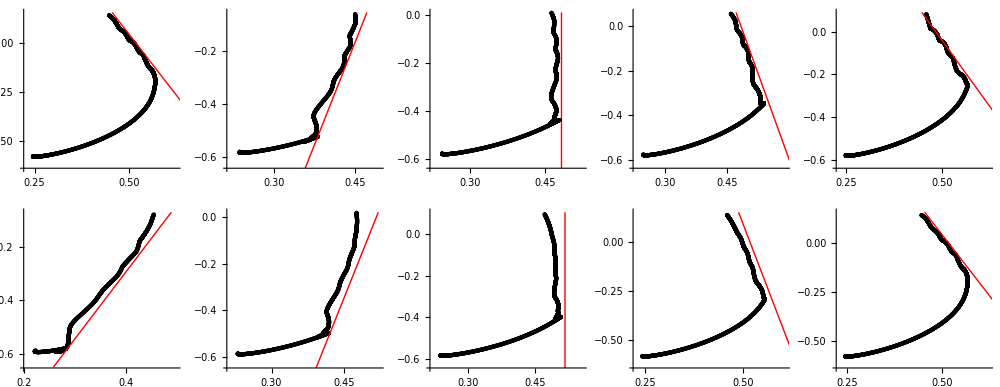

```mathematica
(*Map[GrayLevel,NtoD["NeuralOutput0"]]*)
skip = 3;
range ={{0.2,0.7},{-0.2,0.6}};
origin={range[[1,1]],range[[2,1]]};
PlotLineTraj[t_,options_:{}]:=Module[{p1,p2,r,o},
SetTrial[t];
r=VarRange["x","y",0.1,IntegerPart[t0],IntegerPart[tn]];
o={r[[1,1]],r[[2,1]]};
p1=XYPlot[t,"x","y",Join[options,{PlotRange->r,PlotStyle->{Black},AxesOrigin->o}]] /.Point[args___]:>Point[args,VertexColors->Map[GrayLevel,0.8-0.8*NtoD["NeuralOutput0"]]];
p2= PlotEnvLine[t,Join[options,{PlotRange->r,PlotStyle->{Red}}]];
Show[p1,p2]
];

If[numTrials ≤ 5,
GraphicsRow[Table[PlotLineTraj[i,{AspectRatio->1}],{i,0,4}],ImageSize->800],
GraphicsGrid[Table[PlotLineTraj[i*(numTrials/2)+j,{AspectRatio->1}],{i,0,1},{j,0,-1+numTrials/2}],ImageSize->1000]]
```

Joint angle phase space

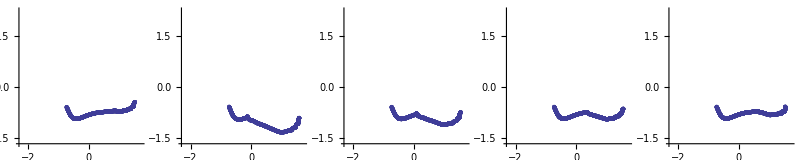

Sensor-shoulder phase space

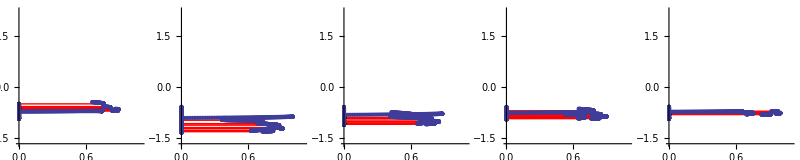

Sensor-elbow phase space

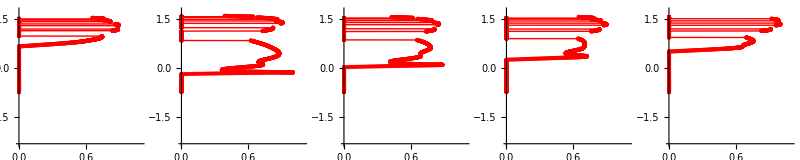

```mathematica
skip = 2;

(*range = {{-1.8,1},{-1.25,1.8}};*)
range=VarRange["angleElbow","angleShoulder",0.1];
origin={range[[1,1]],range[[2,1]]};
Print["Joint angle phase space"]
GraphicsRow[Table[
XYPlotTime[i,"angleElbow","angleShoulder",{AspectRatio->1,PlotRange->range,AxesOrigin->origin}],{i,0,4}],ImageSize->800]

(*range = {{-0.1,1.1},{-1.25,1.8}};*)
range=VarRange["NeuralExtInput0","angleShoulder",0.1];
origin={range[[1,1]],range[[2,1]]};
Print["Sensor-shoulder phase space"]
GraphicsRow[Table[XYPlotTime[i,"NeuralExtInput0","angleShoulder",{AspectRatio->1,PlotRange->range,AxesOrigin->origin}],{i,0,4}],ImageSize->800]

(*range = {{-0.1,1.1},{-1.8,1}};*)
range=VarRange["NeuralExtInput0","angleElbow",0.1];
origin={range[[1,1]],range[[2,1]]};
Print["Sensor-elbow phase space"]
GraphicsRow[Table[XYPlotTime[i,"NeuralState0","angleElbow",{AspectRatio->1,PlotRange->range,PlotStyle->Red,AxesOrigin->origin}],{i,0,4}],ImageSize->800]
```

Single neuron across trials

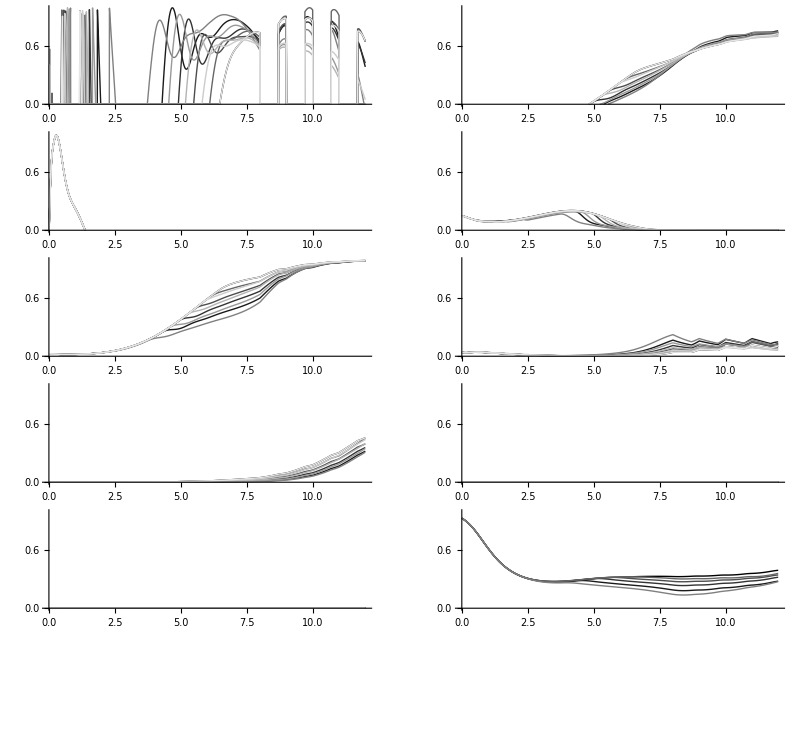

```mathematica
Print["Single neuron across trials"]
n = 4;
skip=0;
PlotAllTrials[var_]:=Show[Table[TimePlotT[var,{PlotStyle->GrayLevel[i/numTrials],PlotRange->{Automatic,{0,1}},AspectRatio->0.3,ImageSize->600,ImagePadding->{{10,0},{20,10}}},i],{i,0,numTrials-1}],ImageSize->800];

GraphicsGrid[
PartitionOdd[Table[PlotAllTrials["NeuralOutput"<>ToString[i]],{i,0,numNeurons-1}]],ImageSize->800]
```

```mathematica
(*Print["All neurons in trials x"]
skip=0;
SetTrial[1];
GraphicsGrid[
Partition[Table[TimePlot["NeuralOutput"<>ToString[i],{PlotStyle->Red,PlotRange->{Automatic,{0,1}},AspectRatio->0.2,ImageSize->600,ImagePadding->{{10,10},{20,10}}}],{i,0,numNeurons-1}],2],ImageSize->800]


Print["OutputNeurons across trials"]
GraphicsGrid[Table[TimePlotT["NeuralOutput"<>ToString[numNeurons-i],{PlotStyle->Red,PlotRange->{Automatic,{0,1}},AspectRatio->0.2,ImagePadding->{{10,10},{20,10}}},j],{j,0,numTrials-1},{i,1,2}],ImageSize->800]
*)
```

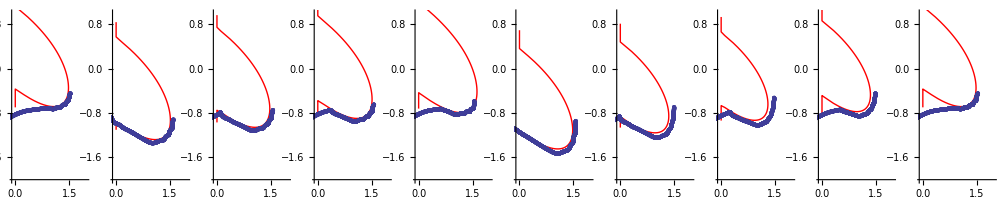

```mathematica
skip=1;
trial = 0;
SetTrial[trial];

PlotAngTraj[tr_]:=Module[{x1,y1,x2,y2,xy,angIntp,angIntPlot,angActPl, angActPl2,range,origin},
SetTrial[tr];
x1=NtoD["lineX1"][[1]];
y1=NtoD["lineY1"][[1]];
x2=NtoD["lineX2"][[1]];
y2=NtoD["lineY2"][[1]];
xy = IntPolLine[x1,y1,x2,y2,100];
angIntp = Map[InvKinP,xy];

angIntPlot=ListPlot[angIntp,Joined->True,PlotStyle->Red]/.Point[args___]:>Point[args,VertexColors->Map[GrayLevel,0.8*Range[0,1,1/100]]];

angActPl=XYPlot[tr,"angleElbow","angleShoulder",{PlotStyle->Black,Joined->True}];
angActPl2=XYPlot[tr,"angleElbow","angleShoulder",{}]/.Point[args___]:>Point[args,VertexColors->Map[GrayLevel,0.8-0.8*NtoD["NeuralOutput0"] ]];

(* get maximum range of line and actual joint trajectory *)
(*range=VarRangeD[ Join[angIntp[[All,1]],NtoD["angleElbow"]],Join[angIntp[[All,2]],NtoD["angleShoulder"]],0.1 ];*)
range={{-0.1,2},{-2,1}};
origin={range[[1,1]],range[[2,1]]};
Show[angIntPlot,angActPl,angActPl2,PlotRange->range,AxesOrigin->origin,AspectRatio->1]
];

GraphicsRow[Table[PlotAngTraj[i],{i,0,numTrials-1}],ImageSize->1000]
```